## Вычисление распада B^0->K^0 μ^+μ^- с учетом резонансных вкладов и с учетом кулоновского взаимодействия между лептонами в конечном состоянии.

## Часть 1. Константы, форм-факторы, Вильсоновские коэффициенты.

### 1) Массы.

Все величины указаны в МэВ. Если не указано обратное, данные взяты из PDG.

```mathematica
MB = 5279.66;

MBs = 5366.92;

me = 0.511;

Mk = 497.614;

Mpi = 134.9768;

Meta = 547.862;

MetaPrime = 957.78;

mmu = 105.658; 

mtau = 1776.86;

mb = 4180;

ms = 93.4;
```

```mathematica
mu = 2.16;
mc = 1270;
```

```mathematica
Γfull = (6.58212 10^-16)/(1.519 10^-12 10^6)
ΓfullBs = (6.58212 10^-16)/(1.520 10^-12 10^6)
```

4.33319×10^-10

4.33034×10^-10

```mathematica
rhat[Mkaon_, Mbmeson_] = (Mkaon/Mbmeson)^2;

mhat[Mlepton_, Mbmeson_] = (Mlepton/Mbmeson)^2;
```

### 2) Постоянная тонкой структуры, константа сильного взаимодействия и постоянная Ферми:

```mathematica
α = 1/137.04;

Gfermi = 1.166 10^-11;

αStr = 0.21;
```

Бегущая константа сильного взаимодействия взята на энергии 5 ГэВ из учебника Пескина и Шредера при нормировочном условии α_s(M_Z) = 0.117

### 3) Элементы матрицы Кабиббо-Кабаяши-Маскавы:

```mathematica
λ = 0.225;
ρ = 0.159;
A = 0.826;
η = 0.348;
```

```mathematica
Vud = 1-λ^2/2;
Vus = λ;
Vub = A λ^3(ρ-I η);

Vcd = -λ;
Vcs = 1-λ^2/2;
Vcb = A λ^2;
```

```mathematica
Vtb = 1;
Vts =-A λ^2;
Vtd = A λ^3(1-ρ-I η);
```

```mathematica
λu[supp_] := (Vub Vus*)/(Vtb Vts*)/; supp=="ts"
λu[supp_] := (Vub Vud*)/(Vtb Vtd*)/; supp=="td"
λc[supp_]:= (Vcb Vcs*)/(Vtb Vts*)/; supp=="ts"
λc[supp_]:= (Vcb Vcd*)/(Vtb Vtd*)/; supp=="td"
```

```mathematica
λu["ts"]+λc["ts"]+1
```

0.0172631+0.0176175 ⅈ

```mathematica
λu["td"]+λc["td"]+1
```

-0.00038547+0.0106336 ⅈ

### 4) Массы и ширины векторных резонансов:

Недостающие ширины взяты из рассчета распада V->l^+l^- на древесном уровне с гамильтонианом взаимодействия H^int(x) = g V^μ(x)l(x)γ_μ l(x) (только он дает удовлетворительные предсказания, ошибаясь не более чем на 10 %).

```mathematica
MJpsi = 3096.900;
ΓJpsi = 92.6 10^-3;
ΓJpsiEE = 0.05971 ΓJpsi; 
ΓJpsiMuMu = 0.05961 ΓJpsi; 
ΓJpsiTauTau = Re[Sqrt[(MJpsi^2 - 4 mtau^2)/(MJpsi^2 - 4 me^2)] (MJpsi^2 + 4 mtau^2)/(MJpsi^2 + 4 me^2)ΓJpsiEE]
```

0.

ψ(2S)-мезон:

```mathematica
MPsi2S = 3686.10;
ΓPsi2S = 0.294;
ΓPsi2SEE = 7.93 10^-3 ΓPsi2S;
ΓPsi2SMuMu = 8 10^-3 ΓPsi2S;
ΓPsi2STauTau = 3.1 10^-3 ΓPsi2S;
```

ψ(3770)-мезон:

```mathematica
MPsi3770 = 3773.7;
ΓPsi3770 = 0.0272;
ΓPsi3770EE = 9.6 10^-6 ΓPsi3770;
ΓPsi3770MuMu = Sqrt[(MPsi3770^2 - 4 mmu^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mmu^2)/(MPsi3770^2 + 4 me^2) ΓPsi3770EE;
ΓPsi3770TauTau = Sqrt[(MPsi3770^2 - 4 mtau^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mtau^2)/(MPsi3770^2 + 4 me^2)ΓPsi3770EE;
```

ψ(4040)-мезон:

```mathematica
MPsi4040 = 4039;
ΓPsi4040 = 0.08;
ΓPsi4040EE = 1.07 10^-5 ΓPsi4040;
ΓPsi4040MuMu = 9 10^-6 ΓPsi4040;
ΓPsi4040TauTau = Sqrt[(MPsi4040^2 - 4 mtau^2)/(MPsi4040^2 - 4 me^2)] (MPsi4040^2 + 4 mtau^2)/(MPsi4040^2 + 4 me^2)ΓPsi4040EE;
```

ψ(4160)-мезон:

```mathematica
MPsi4160 = 4191;
ΓPsi4160 = 0.07;
ΓPsi4160EE = 6.9 10^-6 ΓPsi4160;
ΓPsi4160MuMu = Sqrt[(MPsi4160^2 - 4 mmu^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mmu^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
ΓPsi4160TauTau = Sqrt[(MPsi4160^2 - 4 mtau^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mtau^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
```

ψ(4415)-мезон:

```mathematica
MPsi4415 = 4421;
ΓPsi4415 = 0.062;
ΓPsi4415EE = 9.4 10^-6 ΓPsi4415;
ΓPsi4415MuMu = 2 10^-5 ΓPsi4415;
ΓPsi4415TauTau = Sqrt[(MPsi4415^2 - 4 mtau^2)/(MPsi4415^2 - 4 me^2)] (MPsi4415^2 + 4 mtau^2)/(MPsi4415^2 + 4 me^2)ΓPsi4415EE;
```

ρ(770)-мезон:

```mathematica
Mrho770 = 775.26;
Γrho770 = 149.1;
Γrho770EE = 4.72 10^-5 Γrho770;
Γrho770MuMu = 4.55 10^-5 Γrho770;
Γrho770TauTau = Re[Sqrt[(Mrho770^2 - 4 mtau^2)/(Mrho770^2 - 4 me^2)] (Mrho770^2 + 4 mtau^2)/(Mrho770^2 + 4 me^2)Γrho770EE];
```

ω(782)-мезон:

```mathematica
Momega782 = 782.66;
ΓOmega782 = 8.68;
ΓOmega782EE = 7.38 10^-5 ΓOmega782;
ΓOmega782MuMu = 7.4 10^-5 ΓOmega782;
ΓOmega782TauTau = Re[Sqrt[(Momega782^2 - 4 mtau^2)/(Momega782^2 - 4 me^2)] (Momega782^2 + 4 mtau^2)/(Momega782^2 + 4 me^2)ΓOmega782EE];
```

### 5) Вспомогательные функции ω(s), h(m, s), h(0, s), H(m,s):

Эти функции необходимы для определения Вильсоновских коэффициентов с учетом резонансного вклада и вклада от c-анти-с петель. Определения взяты из работы [Описание четырехчастичных распадов Bd, s → µ+µ−e+e− в Стандартной Модели// А. В. Данилина Н. В. Никитин] и [Effective Hamiltonian for B  →  X_s e+ e- Beyond Leading Logarithms in the NDR and HV Schemes // A.J. Buras, M. Muenz]

Вспомогательная функция ω(s):

```mathematica
ω[s_] = -2/9 Pi^2 - 4/3 PolyLog[2,s] - 2/3 Log[s]Log[1-s]-(5+4 s)/(3(1+2s))Log[1-s] - (2s(1+s)(1-2s))/(3(1-s)^2(1+2s))Log[s]+(5+9s-6 s^2)/(6(1-s)(1+2s));
```

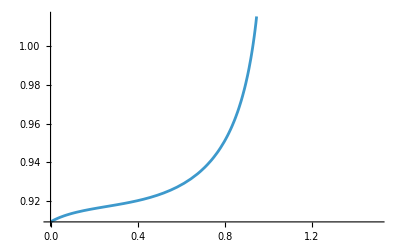

```mathematica
Plot[1+ αStr/Pi ω[s], {s, 0, 1.5}]
```

Вспомогательная функция h(m,s):

```mathematica
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] (Log[Abs[(Sqrt[1-(4 m^2)/s]+1)/(Sqrt[1-(4 m^2)/s]-1)]]-I Pi)/; (4 m^2)/s<=1 /; m!=0
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] 2 ArcTan[1/Sqrt[(4 m^2)/s - 1]]/; (4 m^2)/s>1 /; m!=0
h[m_,s_] :=8/27-4/9 Log[s] + 4/9 I Pi /; m==0
```

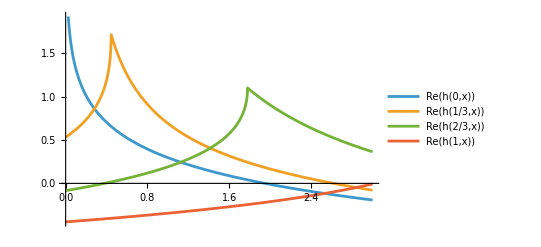

```mathematica
Plot[{Re[h[0,x]],  Re[h[1/3,x]], Re[h[2/3,x]], Re[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

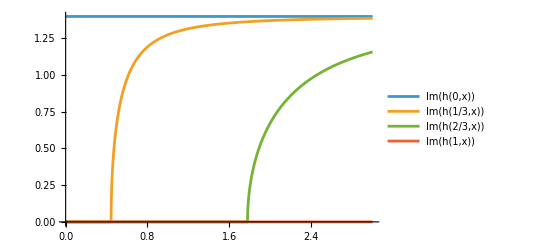

```mathematica
Plot[{Im[h[0,x]],  Im[h[1/3,x]], Im[h[2/3,x]], Im[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

Вспомогательная функция H(m_c,s):

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiEE)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SEE)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770EE)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040EE)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160EE)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415EE)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="e"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiMuMu)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SMuMu)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770MuMu)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040MuMu)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160MuMu)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415MuMu)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="mu"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiTauTau)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2STauTau)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770TauTau)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040TauTau)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160TauTau)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415TauTau)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="tau"
```

```mathematica
Plot[Abs[Hc[1/4.58, x, "mu"]], {x, 0, 1.9}, PlotLabels->"|H(m_c=0,s)|"]
```

-Graphics-

Вспомогательная функция H(m_u,s):

```mathematica
Hu[m_, s_, lep_] := h[m,s]+1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770EE)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782EE)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="e"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]+ 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770MuMu)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782MuMu)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="mu"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]+ 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770TauTau)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782TauTau)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="tau"
```

```mathematica
Plot[Abs[Hu[0.5, x, "mu"]], {x, 0.02, 0.05}, PlotLabels->"|H(m_u=0,s)|"]
```

-Graphics-

### 6) Вильсоновские коэффициенты:

Подразумевается  соглашение C_2(M_W) = -1. Масштабный фактор, на котором берутся значения коэффициентов: μ_0 = 5 ГэВ.

 Численные значения взяты из работ, указывавшихся в пунтке (5) данного раздела.

```mathematica
C1 = 0.241;
C2 = -1.1;
C3 = -0.0104;
C4 = 0.02433;
C5= - 0.00706;
C6 = 0.0294;
C7gamma = 0.312;
C9V = -4.21;
C10A = 4.41;
```

Эффективный коэффициент Вильсона (C_(9V))^eff(μ, s), учитывающий с-анти-с петли, а также вклад резонансов:

```mathematica
C9Veff[s_,Mbmeson_, lep_,supp_] = (1+αStr/Pi ω[s mb^2/Mbmeson^2])C9V - (3C1+C2)(λu[supp] Hu[mu/mb, s,lep] + λc[supp] Hc[(1.2mc)/mb, s,lep])+(3 C3 + C4+ 3 C5+ C6) (2/9 + Hc[(1.2mc)/mb, s,lep])- 1/2(4C3 + 4C4 + 3C5+ C6) h[1, s] - 1/2(C3+ 3C4)h[ms/mb,s];
```

```mathematica
LogPlot[Abs[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.8},  PlotLabels->"|(C_(9  V))^eff(s)|"]
```

-Graphics-

```mathematica
Plot[Im[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Im((C_(9  V))^eff(s))"]
```

-Graphics-

```mathematica
Plot[Re[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Re((C_(9  V))^eff(s))"]
```

-Graphics-

### 7) Форм-факторы:

Численные значения взяты из работы [Weak form factors for heavy meson decays: An update // D. Melikhov and B. Stech]

Погрешности взяты из работ [B → P and B → V Form Factors from B-Meson Light-Cone Sum Rules beyond Leading Twist // N. Gubernari, A. Kokulu, D. van Dyk]
[Bs → Klν and B(s) → π(K)ll decays at large recoil and CKM matrix elements // Alexander Khodjamirian and Aleksey V. Rusov]

Константы f(0), σ_1, σ_2 для распада B^0-> K^0 l^+l^-
1) Для функции F_+(q^2):

```mathematica
FplusBK = 0.35;
DeltaFplusBK = 0.08;
σplus1BK = 0.43;
σplus2BK = 0;
```

2) Для функции F_0(q^2):

```mathematica
F0BK = 0.36;
σ01BK = 0.70;
σ02BK = 0.27;
```

3) Для функции F_T(q^2):

```mathematica
FtBK = 0.358;
DeltaFtBK = 0.08;
σt1BK = 0.43;
σt2BK = 0;
```

```mathematica
MVbk = 5420;
```

Константы f(0), σ_1, σ_2 для распада B^0-> π^0 l^+l^-
1) Для функции F_+(q^2):

```mathematica
FplusBpi = 0.28;
DeltaFplusBpi = 0.07;
σplus1Bpi = 0.48;
σplus2Bpi = 0;
```

2) Для функции F_0(q^2):

```mathematica
F0Bpi = 0.29;
σ01Bpi = 0.76;
σ02Bpi = 0.28;
```

3) Для функции F_T(q^2):

```mathematica
FtBpi = 0.253;
DeltaFtBpi = 0.06;
σt1Bpi = 0.48;
σt2Bpi = 0;
```

```mathematica
MVbpi = 5320;
```

Константы f(0), σ_1, σ_2 для распада B_s^0-> η l^+l^-
1) Для функции F_+(q^2):

```mathematica
FplusBeta = 0.36;
DeltaFplusBeta = 0.07;
σplus1Beta = 0.60;
σplus2Beta = 0.20;
```

2) Для функции F_0(q^2):

```mathematica
F0Beta = 0.36;
σ01Beta = 0.80;
σ02Beta = 0.40;
```

3) Для функции F_T(q^2):

```mathematica
FtBeta = 0.36;
DeltaFtBeta = 0.06;
σt1Beta = 0.58;
σt2Beta = 0.18;
```

```mathematica
MVbeta = 5420;
```

Константы f(0), σ_1, σ_2 для распада B_s^0-> η' l^+l^-
1) Для функции F_+(q^2):

```mathematica
FplusBetaPrime = 0.36;
DeltaFplusBetaPrime = 0.07;
σplus1BetaPrime = 0.60;
σplus2BetaPrime = 0.20;
```

2) Для функции F_0(q^2):

```mathematica
F0BetaPrime = 0.36;
σ01BetaPrime = 0.80;
σ02BetaPrime = 0.45;
```

3) Для функции F_T(q^2):

```mathematica
FtBetaPrime = 0.39;
DeltaFtBetaPrime = 0.06;
σt1BetaPrime = 0.58;
σt2BetaPrime = 0.18;
```

```mathematica
MVbetaPrime = 5420;
```

Константы f(0), σ_1, σ_2 для распада B_s^0-> K^0 l^+l^-
1) Для функции F_+(q^2):

```mathematica
FplusBsK = 0.31;
DeltaFplusBsK = 0.08;
σplus1BsK = 0.63;
σplus2BsK = 0.33;
```

2) Для функции F_0(q^2):

```mathematica
F0BsK = 0.31;
σ01BsK = 0.93;
σ02BsK = 0.70;
```

3) Для функции F_T(q^2):

```mathematica
FtBsK = 0.31;
DeltaFtBsK = 0.08;
σt1BsK = 0.61;
σt2BsK = 0.30;
```

```mathematica
MVBsK = 5320;
```

Определение функций F_+(q^2), F_0(q^2), F_T(q^2):

```mathematica
Fp[s_, Mbmeson_, Mvec_, Fzero_, sigma1_, sigma2_] = Fzero/((1-s (Mbmeson/Mvec)^2)(1-sigma1 s (Mbmeson/Mvec)^2+sigma2 s^2 (Mbmeson/Mvec)^4));
F00[s_, Mbmeson_, Mvec_, Fzero_, sigma1_, sigma2_] =  Fzero/(1-sigma1 s (Mbmeson/Mvec)^2+sigma2 s^2(Mbmeson/Mvec)^4);
FT[s_, Mbmeson_, Mvec_, Fzero_, sigma1_, sigma2_] = Fzero/((1-s (Mbmeson/Mvec)^2)(1-sigma1 s (Mbmeson/Mvec)^2+sigma2 s^2 (Mbmeson/Mvec)^4));
```

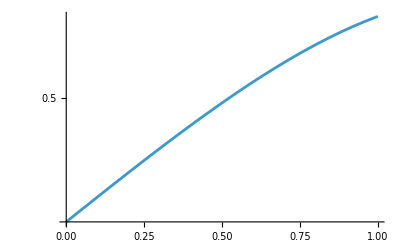

```mathematica
LogPlot[Abs[F00[p, MB, MVbk, F0BK, σ01BK, σ02BK]], {p, 0, 1}]
```

Определение функций f_+(q^2), f_-(q^2), s(q^2):

```mathematica
fp[s_, Mbmeson_, Mvec_, Fzero_, sigma1_, sigma2_] = Fp[s, Mbmeson, Mvec, Fzero, sigma1, sigma2];
fm[s_, Mbmeson_,Mkaon_, Mvec_, Fzero0_, sigma01_, sigma02_, FzeroP_, sigmaP1_, sigmaP2_] =  (1-rhat[Mkaon,Mbmeson])/s(F00[s, Mbmeson, Mvec, Fzero0, sigma01, sigma02] - Fp[s ,Mbmeson, Mvec, FzeroP, sigmaP1, sigmaP2]);
S[s_, Mbmeson_,Mkaon_, Mvec_, Fzero_, sigma1_, sigma2_] = (-FT[s, Mbmeson, Mvec, Fzero, sigma1, sigma2])/(Mbmeson+Mkaon);
```

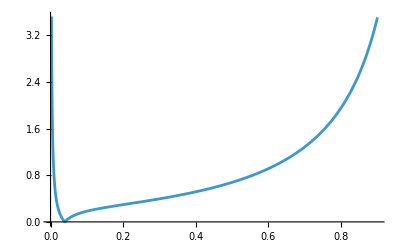

```mathematica
Plot[Abs[fm[p, MB, Mk,MVbk, F0BK, σ01BK, σ02BK, FplusBK, σplus1BK,σplus2BK]], {p, 0, 0.9}]
```

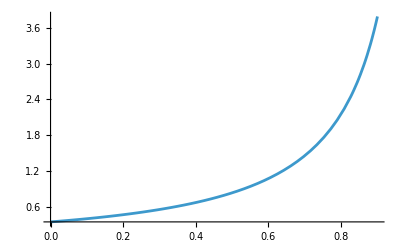

```mathematica
Plot[Abs[fp[p, MB,MVbk, FplusBK, σplus1BK,σplus2BK]], {p, 0, 0.9}]
```

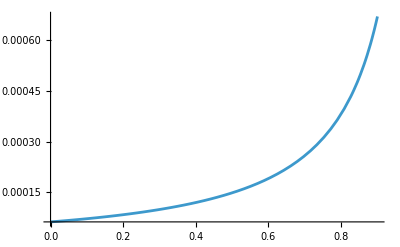

```mathematica
Plot[Abs[S[p, MB,Mk, MVbk, FtBK, σt1BK, σt2BK]], {p, 0, 0.9}]
```

## Часть 2. Дифференциальная ширина, branching ratio.

#### 1) Вспомогательные функции β_p(q^2), δ_p(q^2), ϕ(q^2) = λ(1,s, r), Π(t, s), t(s,cos(θ)):

```mathematica
βp[s_, Mbmeson_,Mkaon_,Mvec_, lep_, supp_, FzeroT_, sigmaT1_, sigmaT2_, FzeroP_, sigmaP1_, sigmaP2_]  = Abs[C9Veff[s Mbmeson^2/mb^2, Mbmeson,lep, supp] fp[ s,Mbmeson, Mvec, FzeroP, sigmaP1, sigmaP2] + 2(mb+ms) C7gamma S[s, Mbmeson,Mkaon, Mvec, FzeroT, sigmaT1, sigmaT2]]^2 + Abs[C10A fp[s,Mbmeson, Mvec, FzeroP, sigmaP1, sigmaP2] ]^2;
δp[s_, Mbmeson_,Mkaon_,Mvec_, Fzero0_, sigma01_, sigma02_, FzeroP_, sigmaP1_, sigmaP2_] = (1+rhat[Mkaon, Mbmeson]-s/2)Abs[fp[s,Mbmeson, Mvec, FzeroP, sigmaP1, sigmaP2]]^2 + (1-rhat[Mkaon, Mbmeson])Re[fp[s,Mbmeson, Mvec, FzeroP, sigmaP1, sigmaP2]Conjugate[fm[s, Mbmeson,Mkaon, Mvec, Fzero0, sigma01, sigma02, FzeroP, sigmaP1, sigmaP2]]]+s/2 Abs[fm[s, Mbmeson,Mkaon, Mvec, Fzero0, sigma01, sigma02, FzeroP, sigmaP1, sigmaP2]]^2;
ϕ[s_, Mbmeson_,Mkaon_] = 1 + rhat[Mkaon, Mbmeson]^2+s^2-2rhat[Mkaon, Mbmeson]-2s-2rhat[Mkaon, Mbmeson] s;
```

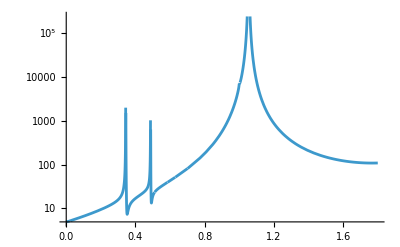

```mathematica
LogPlot[Re[βp[x, MB,Mk,MVbk, "mu", "ts", FtBK, σt1BK, σt2BK,  FplusBK, σplus1BK,σplus2BK]], {x,  0, 1.8}]
```

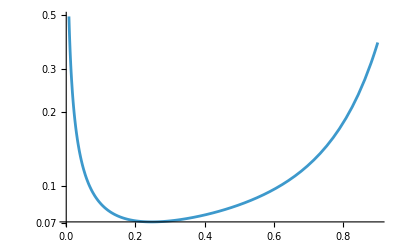

```mathematica
LogPlot[Abs[δp[x, MB,Mk,MVbk, F0BK, σ01BK, σ02BK, FplusBK, σplus1BK,σplus2BK]], {x, 0, 0.9}]
```

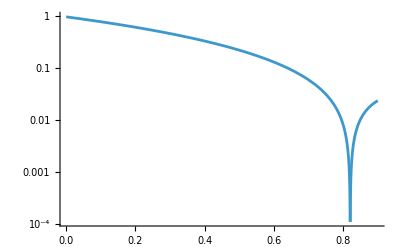

```mathematica
LogPlot[Abs[ϕ[x, MB,Mk ]], {x, 0, 0.9}]
```

```mathematica
tMand[s_,cos_,Mbmeson_, Mkaon_,Mlepton_] = 1/2(1+rhat[Mkaon,Mbmeson]+2 mhat[Mlepton,Mbmeson] - s+Sqrt[ 1-4 mhat[Mlepton,Mbmeson]/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]cos);
Π[s_,cos_,Mbmeson_, Mkaon_,Mlepton_] = (tMand[s,cos,Mbmeson, Mkaon,Mlepton]-1)(tMand[s,cos,Mbmeson, Mkaon,Mlepton]-rhat[Mkaon,Mbmeson])+s tMand[s,cos,Mbmeson, Mkaon,Mlepton] + mhat[Mlepton,Mbmeson](1+rhat[Mkaon,Mbmeson] +mhat[Mlepton,Mbmeson] - s - 2tMand[s,cos,Mbmeson, Mkaon,Mlepton]);
```

#### 2) Кулоновский и полный QED фактор

```mathematica
Clear[Mkaon]
```

```mathematica
Mbm[decay_]:=MB /;MemberQ[{"BKee","BKmumu","BKtautau", "Bpiee", "Bpimumu", "Bpitautau"},decay]
Mbm[decay_]:=MBs /;MemberQ[{"BsKee","BsKmumu","BsKtautau", "Bsetaee","Bsetamumu","Bsetatautau", "BsetaPrimeee","BsetaPrimemumu","BsetaPrimetautau"},decay]

Mlep[decay_]:=me /;MemberQ[{"BKee", "Bpiee", "BsKee", "Bsetaee", "BsetaPrimeee"},decay]
Mlep[decay_]:=mmu /;MemberQ[{"BKmumu", "Bpimumu", "BsKmumu", "Bsetamumu", "BsetaPrimemumu"},decay]
Mlep[decay_]:=mtau /;MemberQ[{"BKtautau", "Bpitautau", "BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
Mkaon[decay_] := Mk /;MemberQ[{"BKee", "BKmumu", "BKtautau","BsKee", "BsKmumu", "BsKtautau"},decay]
Mkaon[decay_] := Mpi /;MemberQ[{"Bpiee", "Bpimumu", "Bpitautau"},decay]
Mkaon[decay_] := Meta /;MemberQ[{"Bsetaee", "Bsetamumu", "Bsetatautau"},decay]
Mkaon[decay_] := MetaPrime /;MemberQ[{"BsetaPrimeee", "BsetaPrimemumu", "BsetaPrimetautau"},decay]
```

```mathematica
V[mRatio_] :=Sqrt[1 - 4 mRatio ] ;
```

```mathematica
Vrel[mRatio_] := V[mRatio]/(1 - 2 mRatio);
```

```mathematica
CAS[s_, decay_] := Abs[Gamma[Sqrt[1/4-α^2]+1/2+I (α/Vrel[mhat[Mlep[decay],Mbm[decay]]/s])]/Gamma[Sqrt[1-4 α^2]+1]]^2 Exp[Pi (α/Vrel[mhat[Mlep[decay],Mbm[decay]]/s])];
Ksoft[ΔE_,s_, decay_]:=(2 (ΔE/Mbm[decay]))^((2 α/Pi)*(1/(4Vrel[mhat[Mlep[decay],Mbm[decay]]/s]))*Log[(1+Vrel[mhat[Mlep[decay],Mbm[decay]]/s])/(1-Vrel[mhat[Mlep[decay],Mbm[decay]]/s])]);
```

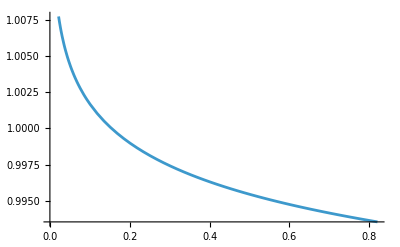

```mathematica
Plot[CAS[s, "BKmumu"]Ksoft[500,s, "BKmumu"], {s, 4mhat[mmu,MB], (1-Mk/MB)^2}]
```

#### 2) Дифференциальная ширина (dΓ_(B->h^0 l^+l^-))/ds распада B->h^0 l^+l^- с кулоновским взаимодействием и без него. Формулы.

```mathematica
VtqVtb[supp_] :=Vts*Vtb/; supp=="ts"
VtqVtb[supp_] :=Vtd*Vtb/; supp=="td"
```

Объяснение переменных:
s = (p_B-p_K)^2/M_B^2 - нормированный на массу B-мезона квадрат переданного импульса

Mbmeson - масса B или B_s мезона

Mkaon - масса псевдоскалярного мезона

Mlepton - масса лептона

lep = {“e”, “mu”, “tau”} - тип лептона (необходим для корректного определения резонансов

supp = {“ts”, “td”} - подавление. Если в распаде наблюдается переход b->t->s, то берем первую переменную, если b->t->d, то вторую

Γfulll - полная ширина распада

FzeroP, sigmaP1, sigmaP2 - параметры форм-фактора F_+(q^2)
Fzero0, sigma01, sigma02 - параметры форм-фактора F_0(q^2)
FzeroT, sigmaT1, sigmaT2 - параметры форм-фактора F_T(q^2)

```mathematica
dBrFreeExtended [s_,Mbmeson_, Mkaon_, Mlepton_,lep_,supp_, Γfulll_, Mvec_, FzeroP_, sigmaP1_, sigmaP2_,Fzero0_, sigma01_, sigma02_, FzeroT_, sigmaT1_, sigmaT2_] = (Gfermi^2 Mbmeson^5 Abs[VtqVtb[supp]]^2 α^2)/(Γfulll 1536 Pi^5)Sqrt[1/4 - mhat[Mlepton,Mbmeson]/s]Sqrt[ϕ[s ,Mbmeson,Mkaon]]((1+(2 mhat[Mlepton,Mbmeson])/s)ϕ[s,Mbmeson,Mkaon]βp[s, Mbmeson,Mkaon,Mvec, lep, supp, FzeroT, sigmaT1, sigmaT2, FzeroP, sigmaP1, sigmaP2] + 12 mhat[Mlepton,Mbmeson] δp[s, Mbmeson,Mkaon,Mvec, Fzero0, sigma01, sigma02, FzeroP, sigmaP1, sigmaP2]);
```

```mathematica
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK - 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKee"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK + 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKee"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK - 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK + 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK -0.5 DeltaFtBK, σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK +0.5 DeltaFtBK, σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == "+"







dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi -0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi - 0.5DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi +0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, mmu,"mu","td", Γfull, MVbpi, FplusBpi -0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi -0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi,  mmu,"mu","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi,  mmu,"mu","td", Γfull, MVbpi, FplusBpi +0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, mtau,"tau","td", Γfull, MVbpi, FplusBpi -0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi - 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi, mtau,"tau","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MB, Mpi,  mtau,"tau","td", Γfull, MVbpi, FplusBpi +0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == "+"






dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta +0.5 DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5  DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta +0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta +0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == "+"




dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime - 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime +0.5  DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == "+"


dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime - 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime + 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == "+"



dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime -0.5  DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime + 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == "+"





dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK -0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK - 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK + 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK -0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK -0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK +0.5  DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == "+"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK -0.5DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK - 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == "-"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK +0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == "+"
```

Парциальная ширина распада без учета кулоновского взаимодействия с вырезанными резонансами. В областях вырезания производится суммирование по левой и правой границе.

```mathematica
dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree[s, decay, boundary]/; s<=(Sqrt[8]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=1/2(dBrFree[(Sqrt[8]1000)^2/Mbm[decay]^2, decay, boundary] +dBrFree[(Sqrt[11]1000)^2/Mbm[decay]^2, decay, boundary]  )/;s>=(Sqrt[8]1000)^2/Mbm[decay]^2/;s<(Sqrt[11]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree[s, decay, boundary]/; s>=(Sqrt[11]1000)^2/Mbm[decay]^2/;s<(Sqrt[12.5]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=1/2(dBrFree[(Sqrt[12.5]1000)^2/Mbm[decay]^2, decay, boundary] +dBrFree[(Sqrt[15]1000)^2/Mbm[decay]^2, decay, boundary]  )/;s>=(Sqrt[12.5]1000)^2/Mbm[decay]^2/;s<(Sqrt[15]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree[s, decay, boundary]/;s>=(Sqrt[15]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]



dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Bpitautau"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=1/2(dBrFree [0.46, decay, boundary]+dBrFree [0.5, decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Bpitautau"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Bpitautau"},decay]

dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=1/2(dBrFree [0.45, decay, boundary]+dBrFree [0.49, decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
dΓfreeConstricted[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
```

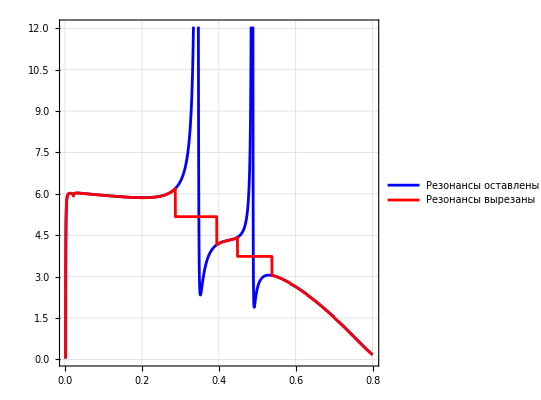

```mathematica
Plot[{10^7 dBrFree[x, "BKmumu", ""]+0.001, 10^7 dΓfreeConstricted[x, "BKmumu", ""]}, {x, 4 mhat[mmu,MB], 0.8},AspectRatio->1,PlotLegends->{"Резонансы оставлены ","Резонансы вырезаны"}, GridLines->Automatic,Frame->True,PlotStyle->{Blue,Red},LabelStyle->Directive[Black,Bold]]
```

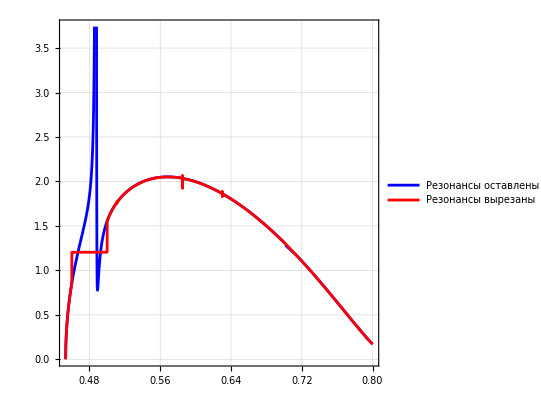

```mathematica
Plot[{10^7 dBrFree[x, "BKtautau", ""]+0.001, 10^7 dΓfreeConstricted[x, "BKtautau", ""]}, {x, 4 mhat[mtau,MB], 0.8},AspectRatio->1,PlotLegends->{"Резонансы оставлены ","Резонансы вырезаны"}, GridLines->Automatic,Frame->True,PlotStyle->{Blue,Red},LabelStyle->Directive[Black,Bold]]
```

```mathematica
dBrCoulomb [s_, decay_, boundary_] = dBrFree[s, decay, boundary]CAS[s, decay];

dΓConstrictedCoulomb [s_, decay_, boundary_] = dΓfreeConstricted[s, decay, boundary]CAS[s, decay];
```

#### 3) Дифференциальная ширина (dΓ_(B->h^0 l^+l^-))/ds распада B->h^0 l^+l^- с кулоновским взаимодействием и без него. Графики.

```mathematica
ClearAll[wthack]
wthack[clr_:Blue][{d___,h_HatchFilling}]:=PatternFilling[ColorReplace[Graphics[{d,h,Rectangle[]}],White->clr],ImageScaled[1]]
opac = 0.3
clr = Black
```

0.3

GrayLevel[0]

```mathematica
resJpsi=(MJpsi/MB)^2;
resPsi2S=(MPsi2S/MB)^2;
BKmumuPlot=Plot[{10^7 dBrFree[s,"BKmumu","-"],1.02 10^7 dBrCoulomb[s,"BKmumu","-"],10^7 dBrFree[s,"BKmumu","+"],1.02 10^7 dBrCoulomb[s,"BKmumu","+"]},{s,4 mhat[mmu,MB],(1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50,clr],Opacity[opac/50,clr]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Thin],PlotRange->{0, 12},Frame->True,AspectRatio->1,LabelStyle->{GrayLevel[0],Bold},Epilog->{{Black,Thick,Dashed,Line[{{resJpsi,0},{resJpsi,100}}],Line[{{resPsi2S,0},{resPsi2S,100}}]}}]
```

-Graphics-

```mathematica
Export["BKmumuPlotv2.pdf",BKmumuPlot,ImageResolution->2000,"CompressionLevel"->0]
```

BKmumuPlotv2.pdf

Распад B->K^0 l^+l^-

```mathematica
PlotsBhll ={{Plot[{10^7 dBrFree[s, "BKee", "-"],1.02 10^7 dBrCoulomb[s, "BKee", "-"],10^7 dBrFree[s, "BKee", "+"],1.02 10^7 dBrCoulomb[s, "BKee", "+"] }, {s, 4mhat[me,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BKmumu", "-"],1.02 10^7 dBrCoulomb[s, "BKmumu", "-"],10^7 dBrFree[s, "BKmumu", "+"],1.02 10^7 dBrCoulomb[s, "BKmumu", "+"] }, {s, 4mhat[mmu,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BKtautau", "-"],1.02 10^7 dBrCoulomb[s, "BKtautau", "-"],10^7 dBrFree[s, "BKtautau", "+"],1.02 10^7 dBrCoulomb[s, "BKtautau", "+"] }, {s, 4mhat[mtau,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},
{Plot[{10^7 dBrFree[s, "Bpiee", "-"],1.02 10^7 dBrCoulomb[s, "Bpiee", "-"],10^7 dBrFree[s, "Bpiee", "+"],1.02 10^7 dBrCoulomb[s, "Bpiee", "+"] }, {s, 4mhat[me,MB], (1-Mpi/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "Bpimumu", "-"],1.02 10^7 dBrCoulomb[s, "Bpimumu", "-"],10^7 dBrFree[s, "Bpimumu", "+"],1.02 10^7 dBrCoulomb[s, "Bpimumu", "+"] }, {s, 4mhat[mmu,MB], (1-Mpi/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "Bpitautau", "-"],1.02 10^7 dBrCoulomb[s, "Bpitautau", "-"],10^7 dBrFree[s, "Bpitautau", "+"],1.02 10^7 dBrCoulomb[s, "Bpitautau", "+"] }, {s, 4mhat[mtau,MB], (1-Mpi/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[s, "Bsetaee", "-"],1.02 10^7 dBrCoulomb[s, "Bsetaee", "-"],10^7 dBrFree[s, "Bsetaee", "+"],1.02 10^7 dBrCoulomb[s, "Bsetaee", "+"] }, {s, 4mhat[me,MBs], (1-Meta/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "Bsetamumu", "-"],1.02 10^7 dBrCoulomb[s, "Bsetamumu", "-"],10^7 dBrFree[s, "Bsetamumu", "+"],1.02 10^7 dBrCoulomb[s, "Bsetamumu", "+"] }, {s, 4mhat[mmu,MBs], (1-Meta/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "Bsetatautau", "-"],1.02 10^7 dBrCoulomb[s, "Bsetatautau", "-"],10^7 dBrFree[s, "Bsetatautau", "+"],1.02 10^7 dBrCoulomb[s, "Bsetatautau", "+"] }, {s, 4mhat[mtau,MBs], (1-Meta/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[s, "BsetaPrimeee", "-"],1.02 10^7 dBrCoulomb[s, "BsetaPrimeee", "-"],10^7 dBrFree[s, "BsetaPrimeee", "+"],1.02 10^7 dBrCoulomb[s, "BsetaPrimeee", "+"] }, {s, 4mhat[me,MBs], (1-MetaPrime/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BsetaPrimemumu", "-"],1.02 10^7 dBrCoulomb[s, "BsetaPrimemumu", "-"],10^7 dBrFree[s, "BsetaPrimemumu", "+"],1.02 10^7 dBrCoulomb[s, "BsetaPrimemumu", "+"] }, {s, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BsetaPrimetautau", "-"],1.02 10^7 dBrCoulomb[s, "BsetaPrimetautau", "-"],10^7 dBrFree[s, "BsetaPrimetautau", "+"],1.02 10^7 dBrCoulomb[s, "BsetaPrimetautau", "+"] }, {s, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[s, "BsKee", "-"],1.02 10^7 dBrCoulomb[s, "BsKee", "-"],10^7 dBrFree[s, "BsKee", "+"],1.02 10^7 dBrCoulomb[s, "BsKee", "+"] }, {s, 4mhat[me,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BsKmumu", "-"],1.02 10^7 dBrCoulomb[s, "BsKmumu", "-"],10^7 dBrFree[s, "BsKmumu", "+"],1.02 10^7 dBrCoulomb[s, "BsKmumu", "+"] }, {s, 4mhat[mmu,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 dBrFree[s, "BsKtautau", "-"],1.02 10^7 dBrCoulomb[s, "BsKtautau", "-"],10^7 dBrFree[s, "BsKtautau", "+"],1.02 10^7 dBrCoulomb[s, "BsKtautau", "+"] }, {s, 4mhat[mtau,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}}
```

#### 4) Парциальная ширина распада B->Kl^+l^- (branching ratio):

1)  Ширина распада  B->K l^+l^-

```mathematica
IntegralsBKee = {Quiet[NIntegrate[dΓfreeConstricted[x,"BKee","-"], {x, 4mhat[me,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BKee","+"], {x, 4mhat[me,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee","-"], {x, 4mhat[me,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee","+"], {x, 4mhat[me,MB], (1-Mk/MB)^2}]]};
ΓfreeBKee = {(IntegralsBKee[[1]]+IntegralsBKee[[2]])/2, (IntegralsBKee[[2]]-IntegralsBKee[[1]])/4,(IntegralsBKee[[3]]+IntegralsBKee[[4]])/2, (IntegralsBKee[[4]]-IntegralsBKee[[3]])/4, 100(IntegralsBKee[[3]]-IntegralsBKee[[1]])/IntegralsBKee[[1]]};
IntegralsBKmumu = {Quiet[NIntegrate[dΓfreeConstricted[x,"BKmumu","-"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BKmumu","+"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKmumu","-"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKmumu","+"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}]]};
ΓfreeBKmumu = {(IntegralsBKmumu[[1]]+IntegralsBKmumu[[2]])/2, (IntegralsBKmumu[[2]]-IntegralsBKmumu[[1]])/4,(IntegralsBKmumu[[3]]+IntegralsBKmumu[[4]])/2, (IntegralsBKmumu[[4]]-IntegralsBKmumu[[3]])/4, 100(IntegralsBKmumu[[3]]-IntegralsBKmumu[[1]])/IntegralsBKmumu[[1]]};
IntegralsBKtautau = {Quiet[NIntegrate[dΓfreeConstricted[x,"BKtautau","-"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BKtautau","+"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKtautau","-"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKtautau","+"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}]]};
ΓfreeBKtautau = {(IntegralsBKtautau[[1]]+IntegralsBKtautau[[2]])/2, (IntegralsBKtautau[[2]]-IntegralsBKtautau[[1]])/2,(IntegralsBKtautau[[3]]+IntegralsBKtautau[[4]])/2, (IntegralsBKtautau[[4]]-IntegralsBKtautau[[3]])/2, 100(IntegralsBKtautau[[3]]-IntegralsBKtautau[[1]])/IntegralsBKtautau[[1]]};
```

2)  Ширина распада  B->π l^+l^-

```mathematica
IntegralsBpiee = {Quiet[NIntegrate[dΓfreeConstricted[x,"Bpiee","-"], {x, 4mhat[me,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bpiee","+"], {x, 4mhat[me,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpiee","-"], {x, 4mhat[me,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpiee","+"], {x, 4mhat[me,MB], (1-Mpi/MB)^2}]]};
ΓfreeBpiee = {(IntegralsBpiee[[1]]+IntegralsBpiee[[2]])/2, (IntegralsBpiee[[2]]-IntegralsBpiee[[1]])/4,(IntegralsBpiee[[3]]+IntegralsBpiee[[4]])/2, (IntegralsBpiee[[4]]-IntegralsBpiee[[3]])/4, 100(IntegralsBpiee[[3]]-IntegralsBpiee[[1]])/IntegralsBpiee[[1]]};

IntegralsBpimumu = {Quiet[NIntegrate[dΓfreeConstricted[x,"Bpimumu","-"], {x, 4mhat[mmu,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bpimumu","+"], {x, 4mhat[mmu,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpimumu","-"], {x, 4mhat[mmu,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpimumu","+"], {x, 4mhat[mmu,MB], (1-Mpi/MB)^2}]]};
ΓfreeBpimumu = {(IntegralsBpimumu[[1]]+IntegralsBpimumu[[2]])/2, (IntegralsBpimumu[[2]]-IntegralsBpimumu[[1]])/4,(IntegralsBpimumu[[3]]+IntegralsBpimumu[[4]])/2, (IntegralsBpimumu[[4]]-IntegralsBpimumu[[3]])/4, 100(IntegralsBpimumu[[3]]-IntegralsBpimumu[[1]])/IntegralsBpimumu[[1]]};
IntegralsBpitautau = {Quiet[NIntegrate[dΓfreeConstricted[x,"Bpitautau","-"], {x, 4mhat[mtau,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bpitautau","+"], {x, 4mhat[mtau,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpitautau","-"], {x, 4mhat[mtau,MB], (1-Mpi/MB)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bpitautau","+"], {x, 4mhat[mtau,MB], (1-Mpi/MB)^2}]]};
ΓfreeBpitautau = {(IntegralsBpitautau[[1]]+IntegralsBpitautau[[2]])/2, (IntegralsBpitautau[[2]]-IntegralsBpitautau[[1]])/4,(IntegralsBpitautau[[3]]+IntegralsBpitautau[[4]])/2, (IntegralsBpitautau[[4]]-IntegralsBpitautau[[3]])/4, 100(IntegralsBpitautau[[3]]-IntegralsBpitautau[[1]])/IntegralsBpitautau[[1]]};
MatrixForm[{ΓfreeBpiee, ΓfreeBpimumu, ΓfreeBpitautau}]
```

(1.17059×10^-8 | 1.43715×10^-9 | 1.19781×10^-8 | 1.47057×10^-9 | 2.32548
1.16654×10^-8 | 1.43141×10^-9 | 1.19368×10^-8 | 1.46471×10^-9 | 2.3268
3.05747×10^-9 | 3.65248×10^-10 | 3.15023×10^-9 | 3.76323×10^-10 | 3.03447)

3)  Ширина распада  B_s->η l^+l^-

```mathematica
IntegralsBetaee = {Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetaee","-"], {x, 4mhat[me,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetaee","+"], {x, 4mhat[me,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetaee","-"], {x, 4mhat[me,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetaee","+"], {x, 4mhat[me,MBs], (1-Meta/MBs)^2}]]};
ΓfreeBetaee = {(IntegralsBetaee[[1]]+IntegralsBetaee[[2]])/2, (IntegralsBetaee[[2]]-IntegralsBetaee[[1]])/4,(IntegralsBetaee[[3]]+IntegralsBetaee[[4]])/2, (IntegralsBetaee[[4]]-IntegralsBetaee[[3]])/4, 100(IntegralsBetaee[[3]]-IntegralsBetaee[[1]])/IntegralsBetaee[[1]]};
IntegralsBetamumu = {Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetamumu","-"], {x, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetamumu","+"], {x, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetamumu","-"], {x, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetamumu","+"], {x, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]]};
ΓfreeBetamumu = {(IntegralsBetamumu[[1]]+IntegralsBetamumu[[2]])/2, (IntegralsBetamumu[[2]]-IntegralsBetamumu[[1]])/4,(IntegralsBetamumu[[3]]+IntegralsBetamumu[[4]])/2, (IntegralsBetamumu[[4]]-IntegralsBetamumu[[3]])/4, 100(IntegralsBetamumu[[3]]-IntegralsBetamumu[[1]])/IntegralsBetamumu[[1]]};
IntegralsBetatautau =  {Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetatautau","-"], {x, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"Bsetatautau","+"], {x, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetatautau","-"], {x, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"Bsetatautau","+"], {x, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]]};
ΓfreeBetatautau = {(IntegralsBetatautau[[1]]+IntegralsBetatautau[[2]])/2, (IntegralsBetatautau[[2]]-IntegralsBetatautau[[1]])/4,(IntegralsBetatautau[[3]]+IntegralsBetatautau[[4]])/2, (IntegralsBetatautau[[4]]-IntegralsBetatautau[[3]])/4, 100(IntegralsBetatautau[[3]]-IntegralsBetatautau[[1]])/IntegralsBetatautau[[1]]};
MatrixForm[{ΓfreeBetaee, ΓfreeBetamumu, ΓfreeBetatautau}]
```

(4.12673×10^-7 | 3.94635×10^-8 | 4.2227×10^-7 | 4.03812×10^-8 | 2.32548
4.11007×10^-7 | 3.92822×10^-8 | 4.20571×10^-7 | 4.01963×10^-8 | 2.32704
7.04655×10^-8 | 6.52258×10^-9 | 7.27978×10^-8 | 6.7386×10^-9 | 3.30948)

4)  Ширина распада  B_s->η ' l^+l^-

```mathematica
IntegralsBetaPrimeee = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimeee","-"], {x, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimeee","+"], {x, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimeee","-"], {x, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimeee","+"], {x, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]]};
ΓfreeBetaPrimeee = {(IntegralsBetaPrimeee[[1]]+IntegralsBetaPrimeee[[2]])/2, (IntegralsBetaPrimeee[[2]]-IntegralsBetaPrimeee[[1]])/4,(IntegralsBetaPrimeee[[3]]+IntegralsBetaPrimeee[[4]])/2, (IntegralsBetaPrimeee[[4]]-IntegralsBetaPrimeee[[3]])/4, 100(IntegralsBetaPrimeee[[3]]-IntegralsBetaPrimeee[[1]])/IntegralsBetaPrimeee[[1]]};
IntegralsBetaPrimemumu = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimemumu","-"], {x, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimemumu","+"], {x, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimemumu","-"], {x, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimemumu","+"], {x, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]]};
ΓfreeBetaPrimemumu = {(IntegralsBetaPrimemumu[[1]]+IntegralsBetaPrimemumu[[2]])/2, (IntegralsBetaPrimemumu[[2]]-IntegralsBetaPrimemumu[[1]])/4,(IntegralsBetaPrimemumu[[3]]+IntegralsBetaPrimemumu[[4]])/2, (IntegralsBetaPrimemumu[[4]]-IntegralsBetaPrimemumu[[3]])/4, 100(IntegralsBetaPrimemumu[[3]]-IntegralsBetaPrimemumu[[1]])/IntegralsBetaPrimemumu[[1]]};
IntegralsBetaPrimetautau = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimetautau","-"], {x, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsetaPrimetautau","+"], {x, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimetautau","-"], {x, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsetaPrimetautau","+"], {x, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]]};
ΓfreeBetaPrimetautau = {(IntegralsBetaPrimetautau[[1]]+IntegralsBetaPrimetautau[[2]])/2, (IntegralsBetaPrimetautau[[2]]-IntegralsBetaPrimetautau[[1]])/4,(IntegralsBetaPrimetautau[[3]]+IntegralsBetaPrimetautau[[4]])/2, (IntegralsBetaPrimetautau[[4]]-IntegralsBetaPrimetautau[[3]])/4, 100(IntegralsBetaPrimetautau[[3]]-IntegralsBetaPrimetautau[[1]])/IntegralsBetaPrimetautau[[1]]};
MatrixForm[{ΓfreeBetaPrimeee, ΓfreeBetaPrimemumu, ΓfreeBetaPrimetautau}]
```

(3.04668×10^-7 | 2.90348×10^-8 | 3.11753×10^-7 | 2.971×10^-8 | 2.32548
3.03185×10^-7 | 2.88738×10^-8 | 3.10241×10^-7 | 2.95458×10^-8 | 2.32746
2.37372×10^-8 | 2.15686×10^-9 | 2.46508×10^-8 | 2.2401×10^-9 | 3.84634)

5)  Ширина распада  B_s->K l^+l^-

```mathematica
IntegralsBsKee = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsKee","-"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsKee","+"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKee","-"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKee","+"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}]]};
ΓfreeBsKee = {(IntegralsBsKee[[1]]+IntegralsBsKee[[2]])/2, (IntegralsBsKee[[2]]-IntegralsBsKee[[1]])/4,(IntegralsBsKee[[3]]+IntegralsBsKee[[4]])/2, (IntegralsBsKee[[4]]-IntegralsBsKee[[3]])/4, 100(IntegralsBsKee[[3]]-IntegralsBsKee[[1]])/IntegralsBsKee[[1]]};
IntegralsBsKmumu  = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsKmumu","-"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsKmumu","+"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKmumu","-"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKmumu","+"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]]};
ΓfreeBsKmumu = {(IntegralsBsKmumu[[1]]+IntegralsBsKmumu[[2]])/2, (IntegralsBsKmumu[[2]]-IntegralsBsKmumu[[1]])/4,(IntegralsBsKmumu[[3]]+IntegralsBsKmumu[[4]])/2, (IntegralsBsKmumu[[4]]-IntegralsBsKmumu[[3]])/4, 100(IntegralsBsKmumu[[3]]-IntegralsBsKmumu[[1]])/IntegralsBsKmumu[[1]]};
IntegralsBsKtautau = {Quiet[NIntegrate[dΓfreeConstricted[x,"BsKtautau","-"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓfreeConstricted[x,"BsKtautau","+"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKtautau","-"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BsKtautau","+"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]]};
ΓfreeBsKtautau = {(IntegralsBsKtautau[[1]]+IntegralsBsKtautau[[2]])/2, (IntegralsBsKtautau[[2]]-IntegralsBsKtautau[[1]])/4,(IntegralsBsKtautau[[3]]+IntegralsBsKtautau[[4]])/2, (IntegralsBsKtautau[[4]]-IntegralsBsKtautau[[3]])/4, 100(IntegralsBsKtautau[[3]]-IntegralsBsKtautau[[1]])/IntegralsBsKtautau[[1]]};
MatrixForm[{ΓfreeBsKee, ΓfreeBsKmumu, ΓfreeBsKtautau}]
```

(1.34974×10^-8 | 1.71308×10^-9 | 1.38113×10^-8 | 1.75291×10^-9 | 2.32548
1.34452×10^-8 | 1.70553×10^-9 | 1.3758×10^-8 | 1.74522×10^-9 | 2.32692
2.55769×10^-9 | 3.16012×10^-10 | 2.641×10^-9 | 3.26304×10^-10 | 3.25728)

```mathematica
IntegralsSoftBKee = {Quiet[NIntegrate[dΓfreeConstricted[x,"BKee",""], {x, 4mhat[Mlep["BKee"],Mbm["BKee"]], (1-Mkaon["BKee"]/Mbm["BKee"])^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee",""], {x, 4mhat[Mlep["BKee"],Mbm["BKee"]], (1-Mkaon["BKee"]/Mbm["BKee"])^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee",""]Ksoft[50, x,"BKee"], {x, 4mhat[Mlep["BKee"],Mbm["BKee"]], (1-Mkaon["BKee"]/Mbm["BKee"])^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee",""]Ksoft[100, x,"BKee"],{x, 4mhat[Mlep["BKee"],Mbm["BKee"]], (1-Mkaon["BKee"]/Mbm["BKee"])^2}]],Quiet[NIntegrate[dΓConstrictedCoulomb[x,"BKee",""]Ksoft[500, x,"BKee"], {x, 4mhat[Mlep["BKee"],Mbm["BKee"]], (1-Mkaon["BKee"]/Mbm["BKee"])^2}]]};
IntegralsSoftBKee
KqedBKee = {IntegralsSoftBKee[[2]]/IntegralsSoftBKee[[1]],IntegralsSoftBKee[[3]]/IntegralsSoftBKee[[1]],IntegralsSoftBKee[[4]]/IntegralsSoftBKee[[1]],IntegralsSoftBKee[[5]]/IntegralsSoftBKee[[1]]}
```

{3.30408×10^-7,3.38091×10^-7,2.89249×10^-7,2.97243×10^-7,3.16669×10^-7}

{1.02325,0.875431,0.899624,0.958418}

```mathematica
Clear[decays]
```

```mathematica
decays={"BKee","BKmumu","BKtautau","Bpiee","Bpimumu","Bpitautau","BsKee","BsKmumu","BsKtautau","Bsetaee","Bsetamumu","Bsetatautau","BsetaPrimeee","BsetaPrimemumu","BsetaPrimetautau"};

results=Table[sMin=4 mhat[Mlep[dec],Mbm[dec]];
sMax=(1-Mkaon[dec]/Mbm[dec])^2;
gammaFree=Quiet[NIntegrate[dΓfreeConstricted[x,dec,""],{x,sMin,sMax}]];
gammaCoul=Quiet[NIntegrate[dΓConstrictedCoulomb[x,dec,""],{x,sMin,sMax}]];
gamma50=Quiet[NIntegrate[dΓConstrictedCoulomb[x,dec,""] Ksoft[50,x,dec],{x,sMin,sMax}]];
gamma100=Quiet[NIntegrate[dΓConstrictedCoulomb[x,dec,""] Ksoft[100,x,dec],{x,sMin,sMax}]];
gamma500=Quiet[NIntegrate[dΓConstrictedCoulomb[x,dec,""] Ksoft[500,x,dec],{x,sMin,sMax}]];
{dec,gammaFree,gammaCoul,gamma50,gamma100,gamma500},{dec,decays}];

kC=Table[{results[[i,1]],results[[i,3]]/results[[i,2]]},{i,Length[results]}];
kQED=Table[{results[[i,1]],results[[i,4]]/results[[i,2]],results[[i,5]]/results[[i,2]],results[[i,6]]/results[[i,2]]},{i,Length[results]}];

Print["Decay\t\t\tK_C\t\tK_QED(50)\tK_QED(100)\tK_QED(500)"];
Do[Print[StringForm["``\t\t``\t\t``\t\t``\t\t``",kC[[i,1]],NumberForm[kC[[i,2]],{Infinity,4}],NumberForm[kQED[[i,2]],{Infinity,4}],NumberForm[kQED[[i,3]],{Infinity,4}],NumberForm[kQED[[i,4]],{Infinity,4}]]],{i,Length[decays]}];
```

Decay			K_C		K_QED(50)	K_QED(100)	K_QED(500)

BKee		1.0233		0.8754		0.8996		0.9584

BKmumu		1.0233		0.9657		0.9755		0.9987

BKtautau		1.0334		1.0206		1.0228		1.0280

Bpiee		1.0233		0.8735		0.8980		0.9575

Bpimumu		1.0233		0.9636		0.9738		0.9978

Bpitautau		1.0303		1.0164		1.0188		1.0245

BsKee		1.0233		0.8739		0.8982		0.9574

BsKmumu		1.0233		0.9645		0.9745		0.9980

BsKtautau		1.0326		1.0194		1.0217		1.0270

Bsetaee		1.0233		0.8743		0.8986		0.9575

Bsetamumu		1.0233		0.9649		0.9748		0.9982

Bsetatautau		1.0331		1.0201		1.0223		1.0276

BsetaPrimeee		1.0233		0.8761		0.9000		0.9583

BsetaPrimemumu		1.0233		0.9667		0.9763		0.9990

BsetaPrimetautau		1.0385		1.0266		1.0286		1.0334

#### 5) Угловые распределения.

```mathematica
dBrAngleFreeExtended [s_,cos_, Mbmeson_, Mkaon_, Mlepton_,lep_,supp_, Γfulll_, Mvec_, FzeroP_, sigmaP1_, sigmaP2_,Fzero0_, sigma01_, sigma02_, FzeroT_, sigmaT1_, sigmaT2_] = (Gfermi^2 Mbmeson^5 Abs[VtqVtb[supp]]^2 α^2)/(Γfulll 256 Pi^5)(-Π[s,cos,Mbmeson, Mkaon,Mlepton] βp[s, Mbmeson,Mkaon,Mvec, lep, supp, FzeroT, sigmaT1, sigmaT2, FzeroP, sigmaP1, sigmaP2] + 2 mhat[Mlepton,Mbmeson] Abs[C10A]^2 δp[s, Mbmeson,Mkaon,Mvec, Fzero0, sigma01, sigma02, FzeroP, sigmaP1, sigmaP2])Sqrt[1/4 - mhat[Mlepton, Mbmeson]/s] Sqrt[ϕ[s,Mbmeson, Mkaon]]/2;
```

```mathematica
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK - 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKee"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, me,"e","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK + 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKee"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK - 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mmu,"mu","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK + 0.5DeltaFtBK, σt1BK, σt2BK]/; decay=="BKmumu"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK -0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK -0.5 DeltaFtBK, σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK , σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK , σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mk, mtau,"tau","ts", Γfull, MVbk, FplusBK +0.5DeltaFplusBK, σplus1BK,σplus2BK,F0BK, σ01BK, σ02BK, FtBK +0.5 DeltaFtBK, σt1BK, σt2BK]/; decay=="BKtautau"/; boundary == "+"







dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi -0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi - 0.5DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, me,"e","td", Γfull, MVbpi, FplusBpi +0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpiee"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, mmu,"mu","td", Γfull, MVbpi, FplusBpi -0.5DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi -0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi,  mmu,"mu","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi,  mmu,"mu","td", Γfull, MVbpi, FplusBpi +0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpimumu"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, mtau,"tau","td", Γfull, MVbpi, FplusBpi -0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi - 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi, mtau,"tau","td", Γfull, MVbpi, FplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi , σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MB, Mpi,  mtau,"tau","td", Γfull, MVbpi, FplusBpi +0.5 DeltaFplusBpi, σplus1Bpi,σplus2Bpi,F0Bpi, σ01Bpi, σ02Bpi, FtBpi + 0.5 DeltaFtBpi, σt1Bpi, σt2Bpi]/; decay=="Bpitautau"/; boundary == "+"






dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, me,"e","ts", ΓfullBs, MVbeta, FplusBeta +0.5 DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5  DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetaee"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mmu,"mu","ts", ΓfullBs, MVbeta, FplusBeta +0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetamumu"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta -0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta -0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta , σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta , σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Meta, mtau,"tau","ts", ΓfullBs, MVbeta, FplusBeta +0.5DeltaFplusBeta, σplus1Beta,σplus2Beta,F0Beta, σ01Beta, σ02Beta, FtBeta +0.5 DeltaFtBeta, σt1Beta, σt2Beta]/; decay=="Bsetatautau"/; boundary == "+"




dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime - 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, me,"e","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime +0.5  DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimeee"/; boundary == "+"


dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime - 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mmu,"mu","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime + 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimemumu"/; boundary == "+"



dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime -0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime -0.5  DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime , σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime , σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, MetaPrime, mtau,"tau","ts", ΓfullBs, MVbetaPrime, FplusBetaPrime +0.5 DeltaFplusBetaPrime, σplus1BetaPrime,σplus2BetaPrime,F0BetaPrime, σ01BetaPrime, σ02BetaPrime, FtBetaPrime + 0.5 DeltaFtBetaPrime, σt1BetaPrime, σt2BetaPrime]/; decay=="BsetaPrimetautau"/; boundary == "+"





dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK -0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK - 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, me,"e","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK + 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKee"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK -0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK -0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mmu,"mu","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK +0.5  DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKmumu"/; boundary == "+"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK -0.5DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK - 0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == "-"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK , σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK , σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos, MBs, Mk, mtau,"tau","td", ΓfullBs, MVBsK, FplusBsK +0.5 DeltaFplusBsK, σplus1BsK,σplus2BsK,F0BsK, σ01BsK, σ02BsK, FtBsK +0.5 DeltaFtBsK, σt1BsK, σt2BsK]/; decay=="BsKtautau"/; boundary == "+"
```

```mathematica
PlotsBhll3D = {{Plot3D[10^7 dBrAngleFree [s, cos, "BKee", ""], {s,4mhat[me, MB], (1-Mk/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BKmumu", ""], {s,4mhat[mmu, MB], (1-Mk/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BKtautau", ""], {s,4mhat[mtau, MB], (1-Mk/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},{Plot3D[10^7 dBrAngleFree [s, cos, "Bpiee", ""], {s,4mhat[me, MB], (1-Mpi/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "Bpimumu", ""], {s,4mhat[mmu, MB], (1-Mpi/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "Bpitautau", ""], {s,4mhat[mtau, MB], (1-Mpi/MB)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},{Plot3D[10^7 dBrAngleFree [s, cos, "Bsetaee", ""], {s,4mhat[me, MBs], (1-Meta/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "Bsetamumu", ""], {s,4mhat[mmu, MBs], (1-Meta/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "Bsetatautau", ""], {s,4mhat[mtau, MBs], (1-Meta/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},{Plot3D[10^7 dBrAngleFree [s, cos, "BsetaPrimeee", ""], {s,4mhat[me, MBs], (1-MetaPrime/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BsetaPrimemumu", ""], {s,4mhat[mmu, MBs], (1-MetaPrime/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BsetaPrimetautau", ""], {s,4mhat[mtau, MBs], (1-MetaPrime/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},{Plot3D[10^7 dBrAngleFree [s, cos, "BsKee", ""], {s,4mhat[me, MBs], (1-Mk/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BsKmumu", ""], {s,4mhat[mmu, MBs], (1-Mk/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^7 dBrAngleFree [s, cos, "BsKtautau", ""], {s,4mhat[mtau, MBs], (1-Mk/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]}}
```

```mathematica
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree[s, cos, decay, boundary]/; s<=(Sqrt[8]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree[(Sqrt[8]1000)^2/Mbm[decay]^2,cos, decay, boundary] +dBrAngleFree[(Sqrt[11]1000)^2/Mbm[decay]^2, cos,decay, boundary]  )/;s>=(Sqrt[8]1000)^2/Mbm[decay]^2/;s<(Sqrt[11]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree[s,cos, decay, boundary]/; s>=(Sqrt[11]1000)^2/Mbm[decay]^2/;s<(Sqrt[12.5]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree[(Sqrt[12.5]1000)^2/Mbm[decay]^2, cos,decay, boundary] +dBrAngleFree[(Sqrt[15]1000)^2/Mbm[decay]^2,cos, decay, boundary]  )/;s>=(Sqrt[12.5]1000)^2/Mbm[decay]^2/;s<(Sqrt[15]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree[s, cos,decay, boundary]/;s>=(Sqrt[15]1000)^2/Mbm[decay]^2/;MemberQ[{"BKee","BKmumu", "Bpiee", "Bpimumu","BsKee","BsKmumu", "Bsetaee","Bsetamumu", "BsetaPrimeee","BsetaPrimemumu"},decay]



dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Bpitautau"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [0.46,cos, decay, boundary]+dBrAngleFree [0.5, cos,decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Bpitautau"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Bpitautau"},decay]

dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree [s, cos,decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
dΓAnglefreeConstricted[s_, cos_,decay_, boundary_] :=1/2(dBrAngleFree [0.45, cos,decay, boundary]+dBrAngleFree [0.49, cos,decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
dΓAnglefreeConstricted[s_,cos_, decay_, boundary_] :=dBrAngleFree [s, cos,decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsetatautau", "BsetaPrimetautau"},decay]
```

```mathematica
dΓAngleConstrictedCoulomb [s_,cos_, decay_, boundary_] = dΓAnglefreeConstricted[s,cos, decay, boundary]CAS[s, decay];
```

```mathematica
Plot3D[10^7 dΓAnglefreeConstricted [s, cos, "BsKmumu", ""], {s,4mhat[mmu, MBs], (1-Mk/MBs)^2}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]
```

```mathematica
Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
PlotsBhllAngleBK = {Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKee", "-"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKee", "-"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKee", "+"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKee", "+"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKmumu", "-"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKmumu", "-"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKmumu", "+"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKmumu", "+"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

$Aborted

```mathematica
PlotsBhllAngleBpi = {Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpiee", "-"],{s, 4mhat[me,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpiee", "-"],{s, 4mhat[me,MB], (1-Mpi/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpiee", "+"],{s, 4mhat[me,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpiee", "+"],{s, 4mhat[me,MB], (1-Mpi/MB)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpimumu", "-"],{s, 4mhat[mmu,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpimumu", "-"],{s, 4mhat[mmu,MB], (1-Mpi/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpimumu", "+"],{s, 4mhat[mmu,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpimumu", "+"],{s, 4mhat[mmu,MB], (1-Mpi/MB)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpitautau", "-"],{s, 4mhat[mtau,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpitautau", "-"],{s, 4mhat[mtau,MB], (1-Mpi/MB)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bpitautau", "+"],{s, 4mhat[mtau,MB], (1-Mpi/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bpitautau", "+"],{s, 4mhat[mtau,MB], (1-Mpi/MB)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

```mathematica
PlotsBhllAngleBseta = {Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetaee", "-"],{s, 4mhat[me,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetaee", "-"],{s, 4mhat[me,MBs], (1-Meta/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetaee", "+"],{s, 4mhat[me,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetaee", "+"],{s, 4mhat[me,MBs], (1-Meta/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetamumu", "-"],{s, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetamumu", "-"],{s, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetamumu", "+"],{s, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetamumu", "+"],{s, 4mhat[mmu,MBs], (1-Meta/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetatautau", "-"],{s, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetatautau", "-"],{s, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "Bsetatautau", "+"],{s, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "Bsetatautau", "+"],{s, 4mhat[mtau,MBs], (1-Meta/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

```mathematica
PlotsBhllAngleBsetaPrime = {Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimeee", "-"],{s, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimeee", "-"],{s, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimeee", "+"],{s, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimeee", "+"],{s, 4mhat[me,MBs], (1-MetaPrime/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimemumu", "-"],{s, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimemumu", "-"],{s, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimemumu", "+"],{s, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimemumu", "+"],{s, 4mhat[mmu,MBs], (1-MetaPrime/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimetautau", "-"],{s, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimetautau", "-"],{s, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsetaPrimetautau", "+"],{s, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsetaPrimetautau", "+"],{s, 4mhat[mtau,MBs], (1-MetaPrime/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

```mathematica
PlotsBhllAngleBsK = {Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKee", "-"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKee", "-"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKee", "+"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKee", "+"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKmumu", "-"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKmumu", "-"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKmumu", "+"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKmumu", "+"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKtautau", "-"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKtautau", "-"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dΓAnglefreeConstricted[s,cos, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dΓAngleConstrictedCoulomb[s,cos, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

#### 6) Результаты

```mathematica
TableForm[PlotsBhll]
```

```mathematica
Export["BhLLv2.pdf",TableForm[PlotsBhll],ImageResolution->2000,"CompressionLevel"->0]
```

BhLLv2.pdf

```mathematica
TableForm[PlotsBhll3D]
```

```mathematica
Export["BhLL3D.pdf",TableForm[PlotsBhll3D],ImageResolution->2000,"CompressionLevel"->0]
```

BhLL3D.pdf

```mathematica
TableForm[{PlotsBhllAngleBK,PlotsBhllAngleBpi,PlotsBhllAngleBseta,PlotsBhllAngleBsetaPrime,PlotsBhllAngleBsK}]
```

```mathematica
Export["BhLLangle.pdf",TableForm[{PlotsBhllAngleBK,PlotsBhllAngleBpi,PlotsBhllAngleBseta,PlotsBhllAngleBsetaPrime,PlotsBhllAngleBsK}],ImageResolution->2000,"CompressionLevel"->0]
```

BhLLangle.pdf

```mathematica
TableForm[{PlotsBhllAngleBseta,PlotsBhllAngleBsetaPrime}]
```

```mathematica
Export["BhLLangleNew1.pdf",TableForm[{PlotsBhllAngleBseta,PlotsBhllAngleBsetaPrime}],ImageResolution->2000,"CompressionLevel"->0]
```

BhLLangleNew1.pdf

```mathematica
MatrixForm[{{ΓfreeBKee, ΓfreeBKmumu, ΓfreeBKtautau} ,{ΓfreeBpiee, ΓfreeBpimumu, ΓfreeBpitautau} ,{ΓfreeBetaee, ΓfreeBetamumu, ΓfreeBetatautau},{ΓfreeBetaPrimeee, ΓfreeBetaPrimemumu, ΓfreeBetaPrimetautau},{ΓfreeBsKee, ΓfreeBsKmumu, ΓfreeBsKtautau}}]
```

((3.34713×10^-7
3.7716×10^-8
3.42497×10^-7
3.85931×10^-8
2.32548) | (3.33219×10^-7
3.75236×10^-8
3.40973×10^-7
3.83969×10^-8
2.32723) | (5.0161×10^-8
1.08711×10^-8
5.1838×10^-8
1.12348×10^-8
3.3426)
(1.17059×10^-8
1.43715×10^-9
1.19781×10^-8
1.47057×10^-9
2.32548) | (1.16654×10^-8
1.43141×10^-9
1.19368×10^-8
1.46471×10^-9
2.3268) | (3.05747×10^-9
3.65248×10^-10
3.15023×10^-9
3.76323×10^-10
3.03447)
(4.12673×10^-7
3.94635×10^-8
4.2227×10^-7
4.03812×10^-8
2.32548) | (4.11007×10^-7
3.92822×10^-8
4.20571×10^-7
4.01963×10^-8
2.32704) | (7.04655×10^-8
6.52258×10^-9
7.27978×10^-8
6.7386×10^-9
3.30948)
(3.04668×10^-7
2.90348×10^-8
3.11753×10^-7
2.971×10^-8
2.32548) | (3.03185×10^-7
2.88738×10^-8
3.10241×10^-7
2.95458×10^-8
2.32746) | (2.37372×10^-8
2.15686×10^-9
2.46508×10^-8
2.2401×10^-9
3.84634)
(1.34974×10^-8
1.71308×10^-9
1.38113×10^-8
1.75291×10^-9
2.32548) | (1.34452×10^-8
1.70553×10^-9
1.3758×10^-8
1.74522×10^-9
2.32692) | (2.55769×10^-9
3.16012×10^-10
2.641×10^-9
3.26304×10^-10
3.25728))